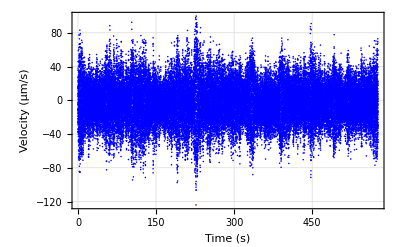

yyV1.png

```mathematica
data=Import["D:\\data_collection\\2-14-23\\Seismometer data\\Data\\XX.S0001..HHY_centaur-6_8725_20230217_080000.txt","Table"];
x=(data[[All,1]]);
y=data[[All,2]];
ListPlot[Transpose[{x,y/((6*10^2))}],PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Time (s)","Velocity (μm/s)"},Frame->True, PlotStyle->Blue,LabelStyle->{12,GrayLevel[0],Bold}]
Export["yyV1.png",ListPlot[Transpose[{x,y/((6*10^2))}],PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Time (s)","Velocity (μm/s)"},Frame->True, PlotStyle->Blue,LabelStyle->{12,GrayLevel[0],Bold}]]
```

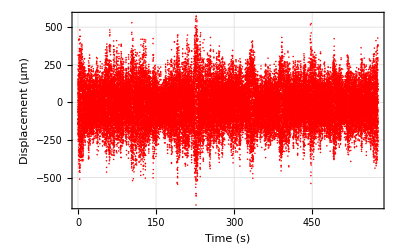

yyD1.png

yyA1.png

0

```mathematica
intg=Table[(y[[var]]+y[[var-1]])*(0.01)/2,{var,1,Length[y]}];
ListPlot[Transpose[{x,intg}],PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Time (s)","Displacement (μm)"},Frame->True,PlotStyle->Red,LabelStyle->{12,GrayLevel[0],Bold}]
Export["yyD1.png",ListPlot[Transpose[{x,intg}],PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Time (s)","Displacement (μm)"},Frame->True,PlotStyle->Red,LabelStyle->{12,GrayLevel[0],Bold}]]
Export["yyA1.png",ListPlot[Transpose[{x,intg*0.03}],PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Time (s)"," Local Gravity Projection (pm/s^2)"},Frame->True,PlotStyle->Orange,LabelStyle->{12,GrayLevel[0],Bold}]]
```